```mathematica
n:= 30
```

```mathematica
X:= TransformedDistribution[2x-n,x\[Distributed]BinomialDistribution[n,1/2]]
```

```mathematica
Y:= TransformedDistribution[2x-n,x\[Distributed]NormalDistribution[n*0.5,Sqrt[n*0.25]]]
```

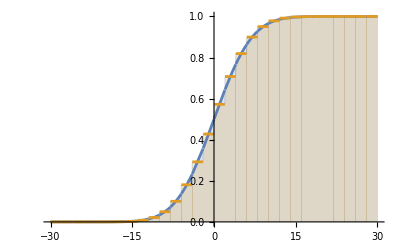

```mathematica
Plot[{CDF[Y,z],CDF[X,z]},{z,-n,n}, Filling->Axis]
```